IAS 2018 
Jouko Teeriaho
Lappland UAS

# Elliptic Curve Cryptography with Mathematica implementations

## 1. Structure of a modern cryptosystem

Cryptosystem is a software which includes 1) authentication, 2) key exchange 
3) symmetric encryption algorithm and 4) digital signature algorithm

For 1,2 and 4  it uses typically public key algorithms like RSA or ECC 
and for 3 (data encryption) symmetric key algorithm (AES)

### Functions needed of a cryptosystem like SSL

-Graphics-

Earlier standard:  RSA authentication, RSA Key Exchange, 
Sha256RSA digital signature,  AES block cipher

Today’s standard is based on Elliptic Curve cryptography, which provides
authentication, key exchange and digital signatures

### ECC reduces safe key lenghts 90% compared to RSA

EU recommendation from 2008 shows how large keys RSA needs to provide security
Increasing of safe key lenghts means performance and capacity problems.

-Graphics-

### => ECC (Elliptic Curve Cryptography) provides equal security with much smaller key lengths than RSA.

## 2. Algebraic concepts

ECC belongs to a larger family, called cyclic group cryptography

### Groups

A set G  together with an operation * defined in G, is called a group if

G1    a*b ∈ G  			for all a, b ϵ G
G2    a*(b*c) = (a*b)*c 	for all  a,b,c in G
G3    There exists a “neutral element” e ∈ G  with property  
	a*e = e*a = a  for all a ∈ G    
G4    For every a ∈ G , there exists  a^-1∈ G  with property a*a^-1=a^-1*a = e    
( inverse element)

### Commutative groups are called Abelian groups

If  a*b = b*a for all a*b ∈ G, G is called an "Abelian group"

### Finite groups have finite number of elements

Let n = #G = number of elements in G  . Then

g^n  =  e   for  all  g ∈ G

### Subgroups is a group within a group

A subset  H  of a group G , where H is self a group,  is called a subgroup of G

### Lagrange's theorem gives possible subgroup sizes

The number of elements of a subgroup H of a finite group G  divides the number of elements of G
		
		#H = #G / d        for some integer d

### Cyclic groups are groups derived from one elements

A finite group G of n elements is cyclic , if  there exist an element  ( or elements) g ∈ G  with 

		{ g, g^2, ... ,   g^n = e}  = G
Element g is called a "generator"  of  group G  

(Comment:  Fact that g^n= e  is called Euler’s theorem)

#### Order of an element

The subgroup generated by element a is denoted by <a>. 
Its size is called order of a, Ord(a)

Thus for generators of G,   Ord(g) = #G  (size of G)

## 3. Cyclic groups on Elliptic curves

For a long time mathematicians have known that there exists group structures on certain curves.
Cryptography has found specially groups on Elliptic Curves useful.

### Definition of Elliptic Curves

In the 1880's Weierstrass explored curves of form 

		y^2 + A xy  =  x^3  + B x^2  + C x +   D

They are called elliptic curves.

#### Elliptic curves used in cryptography

By simple coordinate transformations it is possible to reduce the form of elliptic curves to following

y^2  = x^3  +  a x +  b

#### Animation of elliptic curves shows how elliptic curves look like

```mathematica
Manipulate[ContourPlot[y^2==x^3-3 x+b,{x,-3,5},{y,-5,5},Axes->True],{b,-5,5}]
```

Curves, where the right hand side polynomial has double roots, have no group structure. (see picture below)

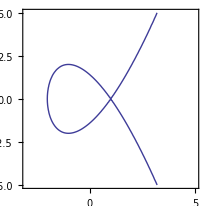

Group operation between points of the curve

-Graphics-

### Existence of a neutral element O and inverse element -P

-Graphics-

Neutral element O is a point with y = ∞ , which is added to the 
curve to complete its group structure.

## 4. Discrete Elliptic Curves - Mathematica implementation

### Discrete elliptic curves over finite fields F_q

Discrete Elliptic curve consists of all points (x,y), where x and y are integers between 1...(q -1)  where q is prime.    All calculations are performed mod q.

E(F_q) =  set of all integer pairs (x, y) , where 0 ≤ x,y < q  satisfying 
equation   y^2 = x^3 + a x + b   (mod q)

## Example : Elliptic Curve y^2= x^3-3x+99 over F_281

#### Listing the points of the curve

```mathematica
q=281; pts={};
For[x=0,x<q,x++,
For[y=0,y<q,y++,
If[Mod[y^2-(x^3-3x+99),q]==0,pts=Append[pts,{x,y}]]]]
pts //StandardForm
```

{{2,35},{2,246},{5,107},{5,174},{6,4},{6,277},{7,126},{7,155},{8,5},{8,276},{11,58},{11,223},{13,3},{13,278},{14,122},{14,159},{15,30},{15,251},{16,139},{16,142},{19,88},{19,193},{23,26},{23,255},{26,52},{26,229},{27,84},{27,197},{28,7},{28,274},{30,95},{30,186},{32,52},{32,229},{33,44},{33,237},{34,47},{34,234},{35,88},{35,193},{36,1},{36,280},{38,129},{38,152},{39,65},{39,216},{42,57},{42,224},{44,17},{44,264},{45,56},{45,225},{48,26},{48,255},{49,108},{49,173},{51,33},{51,248},{55,111},{55,170},{56,22},{56,259},{57,137},{57,144},{60,119},{60,162},{65,58},{65,223},{66,55},{66,226},{67,122},{67,159},{68,13},{68,268},{70,120},{70,161},{73,67},{73,214},{74,112},{74,169},{75,116},{75,165},{77,30},{77,251},{80,57},{80,224},{82,112},{82,169},{84,22},{84,259},{85,69},{85,212},{88,43},{88,238},{89,89},{89,192},{90,14},{90,267},{91,6},{91,275},{92,66},{92,215},{93,123},{93,158},{98,107},{98,174},{100,1},{100,280},{101,90},{101,191},{106,85},{106,196},{107,137},{107,144},{108,56},{108,225},{112,134},{112,147},{115,104},{115,177},{117,137},{117,144},{119,5},{119,276},{122,130},{122,151},{125,112},{125,169},{128,56},{128,225},{129,70},{129,211},{130,91},{130,190},{131,42},{131,239},{132,23},{132,258},{133,128},{133,153},{134,21},{134,260},{135,40},{135,241},{137,36},{137,245},{138,72},{138,209},{140,41},{140,240},{141,22},{141,259},{143,51},{143,230},{145,1},{145,280},{148,127},{148,154},{149,136},{149,145},{151,105},{151,176},{153,49},{153,232},{154,5},{154,276},{156,115},{156,166},{159,57},{159,224},{164,16},{164,265},{165,15},{165,266},{168,40},{168,241},{171,37},{171,244},{172,37},{172,244},{173,49},{173,232},{174,16},{174,265},{175,29},{175,252},{176,60},{176,221},{177,59},{177,222},{178,107},{178,174},{179,134},{179,147},{180,99},{180,182},{182,59},{182,222},{184,113},{184,168},{186,79},{186,202},{189,30},{189,251},{190,64},{190,217},{191,132},{191,149},{192,83},{192,198},{193,63},{193,218},{197,41},{197,240},{199,115},{199,166},{200,122},{200,159},{201,130},{201,151},{203,59},{203,222},{204,66},{204,215},{205,58},{205,223},{207,115},{207,166},{210,26},{210,255},{212,75},{212,206},{213,121},{213,160},{215,71},{215,210},{217,38},{217,243},{218,98},{218,183},{219,37},{219,244},{220,61},{220,220},{223,52},{223,229},{224,16},{224,265},{225,41},{225,240},{226,135},{226,146},{227,88},{227,193},{234,54},{234,227},{236,49},{236,232},{239,130},{239,151},{243,97},{243,184},{244,74},{244,207},{251,100},{251,181},{253,46},{253,235},{254,27},{254,254},{256,2},{256,279},{257,39},{257,242},{259,40},{259,241},{263,28},{263,253},{264,24},{264,257},{266,66},{266,215},{271,134},{271,147},{274,45},{274,236},{278,9},{278,272},{280,35},{280,246}}

#### Addition of Zero Element O completes the group

```mathematica
pts=pts∪{O}
```

#### Calculation of the size of the group

```mathematica
n=Length[pts]
Divisors[n]
```

291

{1,3,97,291}

#### Visualization of the group elements

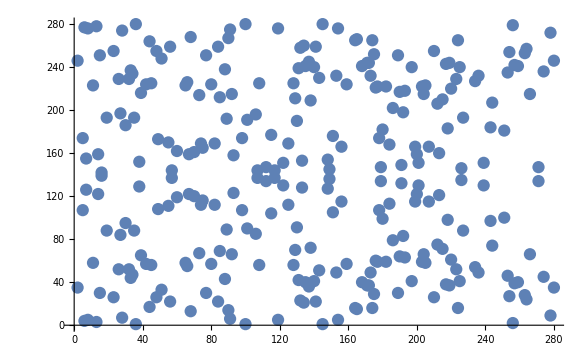

```mathematica
ListPlot[pts,PlotStyle-> PointSize[0.015]]
```

Mathematica Function EllipticSum for group addition

Arguments:	 	q = prime modulus
			a, b are parameters of the curve	y^2 = x^3 + a x + b
			P_list = point P  in form { x, y}
			Q_list = point Q in form { x, y}
EllipticSum  returns the sum P + Q 

Function must also work in special cases, when either P or Q is zero element O,
or P equals Q.

```mathematica
EllipticSum[q_,a_,b_,P_List,Q_List]:=
Module[ {λ,x3,y3,P3},
Which[P=={O}, R=Q,
Q=={O}, R=P,
P[[1]] ≠Q[[1]], 
λ= Mod[(Q[[2]]-P[[2]])*PowerMod[Q[[1]]-P[[1]],-1,q],q];
x3=Mod[λ^2-P[[1]]-Q[[1]],q];
y3=Mod[-(λ (x3-P[[1]])+P[[2]]),q];
R={x3,y3},
(P==Q)∧(P≠{O}),
λ=Mod[ (3*P[[1]]^2+a)*
PowerMod[2 P[[2]],-1,q],q];
x3=Mod[λ^2-2P[[1]],q];
y3=Mod[-(λ (x3-P[[1]])+P[[2]]),q];
R={x3,y3},
(P[[1]]==Q[[1]])∧ (P[[2]]≠Q[[2]]), R={O}];
R]
```

This Mathematica function was originally presented first by Tillman

#### Test 1: Calculate sum of two points: (8,5) + (190, 64)

```mathematica
q=281;P={8,5}; Q={190,64};
EllipticSum[q,-3,99,P,Q]
```

{55,111}

#### Test 2. Addition of Zero element: (8,5) + O should be (8,5)

```mathematica
P={8,5};
EllipticSum[q,-3,99,P,{O}]
```

{8,5}

Mathematica function for calculation multiple nP of point P

Function is a modification of fast exponentiation algorithm PowerMod to ECC.
example:   800 P = 512 P+ 256 P +32P  
=> calculation cost is 9 doublings +  3 additions 
(slow method P + P + ... + P  would cost 800 additions)

```mathematica
Mult[n_,P_,q_,a_,b_]:=Module[{x,A,B},
x=n; A=P; B={O};
While[x>1,
If[OddQ[x],
B=EllipticSum[q,a,b,A,B]; 
x=x-1, 
A=EllipticSum[q,a,b,A,A]; 
x=x/2; 
];
];
A=EllipticSum[q,a,b,A,B]; 
A
]
```

This function is author’s own.

Finding a group generator

```mathematica
d=Divisors[n]           (* possible subgroup sizes are divisors of n *)
```

{1,3,97,291}

According to Lagrange theorem, G is a generator if G, 3G and 97G  ≠  O,  but  291G = O

```mathematica
(* picking randomly one elements and testing if it is a generator *)
candidate={135,241};
Table[Mult[d[[k]],candidate,q,-3,99],{k,1,4}]
```

{{135,241},{134,21},{234,227},{O}}

Thus the order of point (135, 241) is 291 => (135, 241) it is a group generator

#### Visualizing the cyclic group {G, 2G , 3G, ..., 290G} with lines

```mathematica
G={135,241}; q=281;
gr1=Table[Mult[i,G,q,-3,99],{i,1,291}]
```

{{135,241},{92,215},{134,21},{80,57},{98,174},{56,259},{5,174},{190,217},{75,116},{89,89},{180,99},{178,107},{254,254},{253,46},{93,123},{73,67},{130,190},{165,15},{39,216},{239,130},{149,136},{264,24},{220,61},{88,238},{101,90},{257,242},{45,225},{199,166},{91,6},{23,255},{224,16},{66,55},{236,232},{106,196},{11,58},{49,108},{203,59},{193,63},{67,122},{205,58},{179,147},{108,225},{159,57},{77,251},{197,41},{129,211},{42,224},{122,130},{57,144},{36,1},{168,241},{259,40},{119,5},{227,88},{186,79},{184,113},{115,177},{30,95},{175,252},{280,246},{6,277},{34,234},{182,59},{145,1},{15,251},{51,33},{140,41},{201,151},{128,56},{143,230},{141,259},{14,122},{68,13},{38,152},{65,223},{207,166},{84,22},{131,239},{226,135},{218,183},{176,221},{171,37},{132,23},{174,16},{125,112},{16,142},{74,112},{263,253},{133,128},{44,264},{172,37},{223,229},{85,212},{32,229},{173,232},{148,154},{234,227},{55,111},{19,88},{177,222},{215,210},{112,147},{192,198},{156,115},{26,229},{8,5},{274,45},{117,144},{189,30},{210,255},{200,159},{225,240},{7,126},{100,280},{164,265},{256,279},{27,197},{219,37},{82,112},{2,35},{244,74},{191,149},{243,97},{217,243},{266,215},{251,181},{204,66},{153,49},{138,72},{28,7},{60,162},{154,5},{70,120},{107,144},{151,105},{278,272},{33,237},{35,88},{212,206},{48,26},{137,245},{13,3},{271,134},{90,267},{213,160},{213,121},{90,14},{271,147},{13,278},{137,36},{48,255},{212,75},{35,193},{33,44},{278,9},{151,176},{107,137},{70,161},{154,276},{60,119},{28,274},{138,209},{153,232},{204,215},{251,100},{266,66},{217,38},{243,184},{191,132},{244,207},{2,246},{82,169},{219,244},{27,84},{256,2},{164,16},{100,1},{7,155},{225,41},{200,122},{210,26},{189,251},{117,137},{274,236},{8,276},{26,52},{156,166},{192,83},{112,134},{215,71},{177,59},{19,193},{55,170},{234,54},{148,127},{173,49},{32,52},{85,69},{223,52},{172,244},{44,17},{133,153},{263,28},{74,169},{16,139},{125,169},{174,265},{132,258},{171,244},{176,60},{218,98},{226,146},{131,42},{84,259},{207,115},{65,58},{38,129},{68,268},{14,159},{141,22},{143,51},{128,225},{201,130},{140,240},{51,248},{15,30},{145,280},{182,222},{34,47},{6,4},{280,35},{175,29},{30,186},{115,104},{184,168},{186,202},{227,193},{119,276},{259,241},{168,40},{36,280},{57,137},{122,151},{42,57},{129,70},{197,240},{77,30},{159,224},{108,56},{179,134},{205,223},{67,159},{193,218},{203,222},{49,173},{11,223},{106,85},{236,49},{66,226},{224,265},{23,26},{91,275},{199,115},{45,56},{257,39},{101,191},{88,43},{220,220},{264,257},{149,145},{239,151},{39,65},{165,266},{130,91},{73,214},{93,158},{253,235},{254,27},{178,174},{180,182},{89,192},{75,165},{190,64},{5,107},{56,22},{98,107},{80,224},{134,260},{92,66},{135,40},{O}}

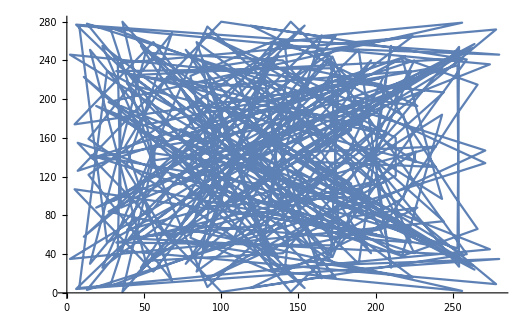

```mathematica
ListPlot[gr1, Joined->True, PlotStyle->PointSize[0.03]]
```

The line goes through all elements of G in order defined by the multiples of g.

## 5. Cryptoalgorithms ECDHE and ElGamal analogy

First we demonstrate algorithms on our example curve

“ECDHE Key Exchange” on the curve  (Diffie Hellman analogy)

1. Alice and Bob generate private keys 

Alices private key :    ka  = 135
Bobs private key:      kb =   222 

2. Alice and Bob send each other their public keys Ya = ka*G and Yb = kb*G

```mathematica
G={135,241};  
q=281;
```

```mathematica
ka=135;  kb=222;
Ya=Mult[ka,G,q,-3,99]
Yb=Mult[kb,G,q,-3,99]
```

{151,105}

{128,225}

3. Both A and B calculate the symmetric key K = ka*kb*G

```mathematica
K=Mult[ka,Yb,q,-3,99]
K=Mult[kb,Ya,q,-3,99]
```

{134,260}

{134,260}

Encryption with Elliptic Curve  (version: ElGamal analogy)

1. Assume that the key K = (K_1,K_2) has been agreed using key exchange presented above 

2.  Message is encoded to pairs of integer,  for example  m = (m_1, m_2) = (100, 120)

3.  Cipher is a “product” of message and key  c = (m_1*K_1 ,  m_2* K_2)  mod q

Comment: This product is neither scalar or vector product. This product is defined by  (a,b)*(c,d) = (a*c , b*d) .    In Mathematica  operator *  performs it,  which makes the Mathematica code short.

```mathematica
m={100,120};  K={134,260};
c=Mod[m*K,q]                (* gives the cipher of message *)
```

{193,9}

Decryption

1.  Recipient calculates the inverse of the key mod q  as follows.  
Decryption key    DK = (K_1^-1 mod q , K_2^-1 mod q)

```mathematica
DK=PowerMod[K,-1,q]
```

{216,107}

2.   Recipient decrypts the cipher using the decryption key DK

```mathematica
Mod[c*DK,q]
```

{100,120}

Result is the same as the original message.

Next we do the same demonstration on a standard curve used in cryptography.

## 6. Demo with NIST’s standard curve P-192

Requirements for curves used in cryptography

1.  The number of points on curve n  should be of form
    n = r*s,   where r is small  ( ≤ 3)  and s is a large prime
  The field modulus q should be ≥ 190 bits  ( security margin)

To be able to determine the order of a point on the curve and find group generators, one has to know the size N of the cyclic group and its divisors (because the order divides) N.

It is difficult to calculate the number of points of a curve.  There is a well known result, 
known as Hasse.b4s inequality from 1933: 
		 | N - (q+1) | ≤ 2√q

N = number of points of the curve,   q = modulus of the underlying Finite Field		 

NIST (National institute of Standards in USA) has standardized 
a group of curves for ECC for cryptographic uses.  
First of them is P-192, which we use in following examples.

### P-192 characteristics

Curve equation y^2= x^3 - 3 x + b 
In the list below G is the group generator, b = parameter of the curve, 
q = modulus , n = size of the cyclic group generated by G

```mathematica
G={602046282375688656758213480587526111916698976636884684818,174050332293622031404857552280219410364023488927386650641};
b=2455155546008943817740293915197451784769108058161191238065;
q=6277101735386680763835789423207666416083908700390324961279;
n=6277101735386680763835789423176059013767194773182842284081;
```

```mathematica
PrimeQ[6277101735386680763835789423176059013767194773182842284081]
```

True

ECC key exchange using P-192

#### Alice generates a private key ka and calculates public key Ya = ka G

```mathematica
ka=2818646689284967968603885680739626753757717668743685369;
Ya=Mult[ka,G,q,-3,b]
```

{4166887439959785442359358401626820195302130396853922747090,342002490943820139356288313636684834682210773457498261724}

#### Bob generates a private key kb and calculates public Yb = kb G

```mathematica
kb=2101924874329080718071957364927874958230913619682994500;
Yb=Mult[kb,G,q,-3,b]
```

{3197479727310441184166659954176065551017813604210849295027,4546651453263495348932303783137537190292590929227544435757}

#### Both Alice and Bob calculate the same point of the curve: K = ka*kb*G

```mathematica
K=Mult[kb,Ya,q,-3,b]          (* Bob's calculation *)
K=Mult[ka,Yb,q,-3,b]           (* Alice's calculation *)
```

{4569158537909585871329893828249154554821121379238590872510,5889543201412998599750263908982414398530518138795041140383}

{4569158537909585871329893828249154554821121379238590872510,5889543201412998599750263908982414398530518138795041140383}

This is a symmetric key produced by the key exchange algorithm

### AES128-key is obtained from this key. Easiest way would be to take first 128 bits of the first component of K

```mathematica
AESkey=Take[IntegerDigits[K[[1]],2],128]
```

{1,0,1,1,1,0,1,0,0,1,0,1,1,0,0,0,0,0,1,1,1,1,0,1,1,0,1,1,0,0,0,1,1,1,1,0,0,1,1,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,0,0,0,1,0,1,1,0,1,1,1,0,0,1,1,0,0,1,1,0,0,0,0,0,1,1,1,0,1,1,0,1,0,0,0,1,0,0,0,1,1,1,1,1,1,0,1,0,1,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0}

Keys are often presented in hexadecimal form

```mathematica
BaseForm[FromDigits[AESkey,2],16]
```

ba583db1e7aa885b9983b447ea910820_16

ECC encryption  (Menezez Vanstone version)

#### Coding message to two component vector

Assume that the message is two words:  (“ArcticSeminar”, “Rovaniemi”)

First we transform message to ASCII and then to two large integers

```mathematica
m01=ToCharacterCode["ArcticSeminar"]
m02=ToCharacterCode["Rovaniemi"]
```

{65,114,99,116,105,99,83,101,109,105,110,97,114}

{82,111,118,97,110,105,101,109,105}

```mathematica
{m1,m2}=Mod[{FromDigits[m01,256],FromDigits[m02,256]},q];
m={m1,m2}
```

{5185232087941534446075041964402,1520664728156487642473}

Encryption is done with operation defined as  
(c1, c2) =  (m1, m2)*(K1, K2) = (m1*K1, m2*K2)

#### Alice encrypts the message

```mathematica
c=Mod[K*m,q]          (* ciphertext *)
```

{2461969853658513928470552774196794839821484524954445766793,4922823632219955069517528447511392059330930252067710373849}

#### Bob calculates decryption key DK and decrypts

```mathematica
DK=PowerMod[K,-1,q]
```

```mathematica
Z=Mod[DK*c,q]
```

{5185232087941534446075041964402,1520664728156487642473}

Bob needs to transform the integers back to cleartext

```mathematica
FromCharacterCode[IntegerDigits[Z[[1]],256]]
FromCharacterCode[IntegerDigits[Z[[2]],256]]
```

ArcticSeminar

Rovaniemi

### Digital signature algorithm ECDSA can also be implemented with Mathematica

## 7. The basis of security of ECC

The hacker knows following information (from certificate and Google)
1) knows the curve which is used
2) knows the group generator point G of the curve
3) knows the modulus q
4) A skilled hacker can find the public keys Ya and Yb from the data stream

For cracking the encryption the hacker would need to solve the private key ka
from equation		
			Ya = ka*G

However this is one of the mathematically “hard problems”.  It is called
ECDLP  :  Elliptic Curve Discrete Logarithm Problem.

For curves used in TLS 1.2  the time which the hacker would need to crack 
the private key from the public key is probably some tens or hundreds of years.